```mathematica
MergeSets[sets1_,sets2_]:=Block[{i,result},
result=Table[Join[sets1[[i]],sets2[[i]]],{i,Length[sets1]}];
result
]
```

```mathematica
KSetPartitions[Range[5],4]
```

{{{1},{2},{3},{4,5}},{{1},{2},{3,4},{5}},{{1},{2},{3,5},{4}},{{1},{2,3},{4},{5}},{{1},{2,4},{3},{5}},{{1},{2,5},{3},{4}},{{1,2},{3},{4},{5}},{{1,3},{2},{4},{5}},{{1,4},{2},{3},{5}},{{1,5},{2},{3},{4}}}

```mathematica
SetsToEdges[sets_]:=Flatten[Map[Map[UndirectedEdge[#[[1]],#[[2]]]&,Subsets[#,{2}]]&,sets]]
```

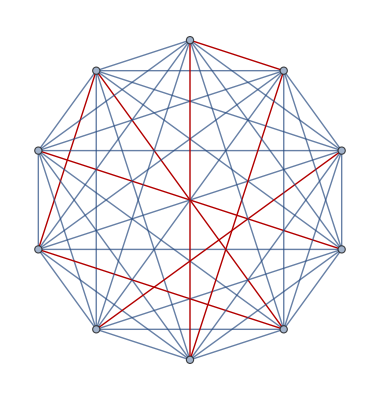
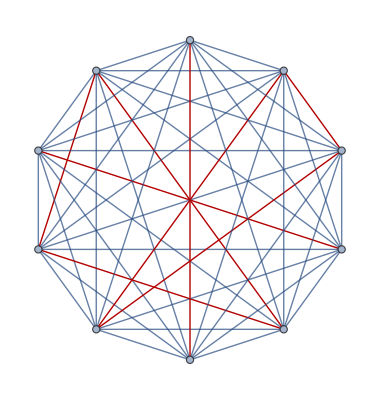
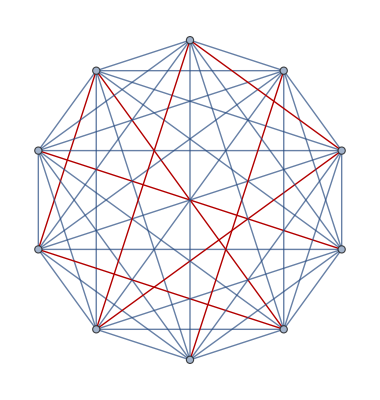
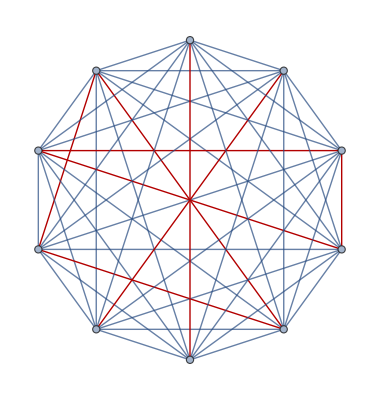
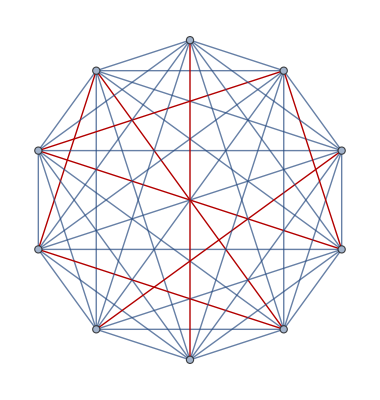
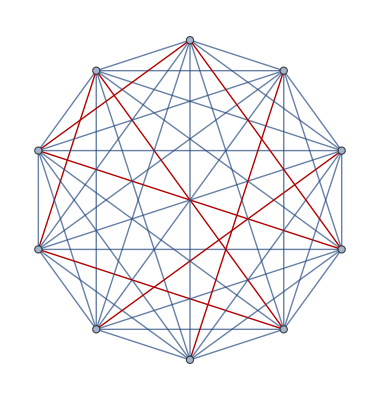
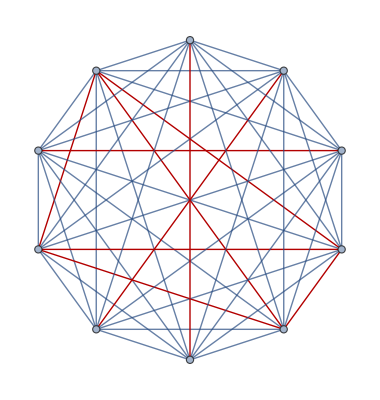
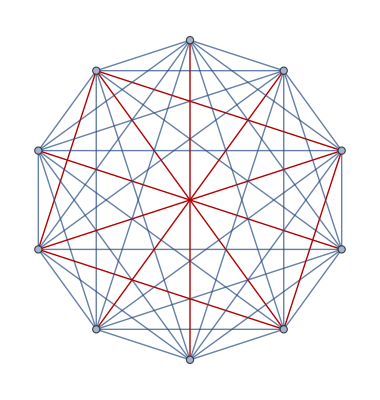

```mathematica
Table[CompleteGraph[10,GraphHighlight->edgeSet],{edgeSet,Table[SetsToEdges[MergeSets[{{1,3},{2},{4},{5}},sets+5]],{sets,KSetPartitions[Range[5],4]}]}]
```

```mathematica
SetsToEdges[{{1,3,6},{2,7,10},{4},{5,9}}]
```

{1<->3,1<->6,3<->6,2<->7,2<->10,7<->10,5<->9}

```mathematica
Monitor[Flatten[With[
{max=10},
With[{edges1=Table[SetsToEdges[MergeSets[{{1,3},{2},{4},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges2=Table[SetsToEdges[MergeSets[{{1,4},{2},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges3=Table[SetsToEdges[MergeSets[{{1},{2,4},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges4=Table[SetsToEdges[MergeSets[{{1},{2,5},{3},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges5=Table[SetsToEdges[MergeSets[{{1},{2},{3,5},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}]
},
Table[
With[{g=EdgeDelete[CompleteGraph[max],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]},
ChromaticPolynomial[g,4]]/24
,{e1,RandomSample[edges1,5]}
,{e2,RandomSample[edges2,5]}
,{e3,RandomSample[edges3,5]}
,{e4,RandomSample[edges4,5]}
,{e5,RandomSample[edges5,5]}
]
]
]]//Tally//Sort,{e1,e2,e3,e4,e5}
]
```

{{9,4},{11,3},{13,1},{15,1},{16,2},{17,1},{18,3},{19,1},{20,11},{21,3},{22,3},{23,1},{24,2},{25,2},{26,17},{27,1},{28,2},{29,10},{30,14},{31,3},{32,10},{33,9},{34,2},{35,5},{36,4},{37,7},{38,5},{39,37},{40,12},{41,15},{44,12},{45,5},{46,11},{47,4},{48,13},{50,9},{51,9},{52,8},{53,10},{54,16},{55,7},{56,4},{57,2},{58,8},{59,6},{60,39},{62,15},{63,3},{64,8},{65,13},{66,25},{67,1},{68,9},{69,12},{70,12},{71,13},{72,19},{73,3},{74,12},{75,14},{76,22},{77,14},{78,7},{79,14},{80,22},{81,1},{82,9},{83,10},{84,22},{85,2},{86,9},{87,16},{88,13},{89,4},{90,24},{91,9},{92,29},{93,5},{94,23},{95,8},{96,16},{97,21},{98,7},{99,12},{100,5},{101,14},{102,26},{103,5},{104,16},{105,35},{106,20},{107,17},{108,9},{109,7},{110,6},{111,8},{112,17},{113,7},{114,15},{115,9},{117,15},{118,23},{119,24},{120,15},{121,12},{122,8},{123,2},{124,12},{125,15},{126,14},{127,7},{128,10},{129,12},{130,11},{131,23},{132,9},{133,7},{134,6},{135,25},{136,11},{137,24},{138,34},{139,5},{140,17},{141,12},{142,23},{143,12},{144,22},{145,37},{146,11},{147,9},{148,6},{149,9},{150,13},{151,7},{152,4},{153,7},{154,6},{155,1},{156,31},{157,5},{158,20},{159,17},{160,7},{161,3},{162,14},{163,21},{164,13},{165,4},{166,16},{167,10},{168,10},{169,5},{170,11},{171,31},{172,14},{173,7},{174,10},{175,1},{176,3},{177,52},{178,3},{179,7},{180,11},{181,4},{182,4},{183,7},{184,16},{185,25},{186,12},{187,11},{188,4},{189,12},{190,16},{191,16},{192,6},{193,3},{194,7},{195,4},{196,6},{197,6},{198,14},{199,11},{200,4},{201,8},{202,9},{203,16},{204,8},{205,10},{206,9},{207,9},{208,3},{210,7},{211,20},{212,9},{213,7},{214,9},{216,12},{217,1},{218,9},{219,9},{220,6},{221,5},{222,4},{223,1},{224,36},{225,14},{226,2},{227,9},{229,2},{230,17},{231,11},{232,4},{233,3},{234,3},{235,1},{236,1},{237,31},{238,11},{239,4},{240,3},{241,2},{242,1},{243,5},{245,7},{246,5},{247,2},{248,23},{249,13},{250,1},{251,5},{252,4},{253,2},{255,6},{256,9},{257,7},{258,5},{259,16},{260,2},{261,4},{262,1},{263,2},{264,10},{265,7},{267,12},{268,3},{269,14},{270,17},{271,1},{272,9},{273,1},{276,17},{277,4},{278,1},{279,17},{280,2},{281,2},{282,9},{283,3},{284,1},{285,2},{286,4},{287,2},{288,21},{289,2},{291,1},{293,8},{294,6},{296,13},{297,11},{300,13},{301,1},{302,7},{303,3},{304,1},{305,1},{306,1},{307,3},{308,2},{310,9},{312,3},{314,8},{315,10},{316,7},{318,10},{319,7},{320,3},{322,1},{324,1},{325,2},{330,2},{332,2},{333,5},{334,1},{336,10},{339,10},{341,2},{342,1},{346,9},{348,1},{349,12},{350,2},{351,4},{352,1},{354,1},{355,3},{356,1},{358,1},{359,2},{360,10},{361,2},{362,2},{363,5},{364,4},{367,10},{368,3},{370,3},{371,3},{375,14},{376,1},{378,3},{380,2},{382,3},{383,3},{384,1},{388,4},{391,1},{393,5},{394,6},{395,1},{399,4},{402,5},{403,5},{404,1},{406,6},{416,1},{419,1},{420,5},{421,1},{423,1},{427,2},{431,2},{432,1},{434,1},{436,1},{438,3},{441,6},{444,4},{446,5},{450,1},{457,1},{458,1},{459,11},{464,1},{465,4},{466,5},{470,1},{471,3},{482,1},{483,1},{484,1},{487,1},{488,2},{490,5},{492,1},{495,4},{498,5},{513,1},{514,1},{516,4},{520,9},{523,1},{540,2},{552,1},{556,1},{570,2},{580,3},{596,1},{599,10},{602,1},{603,5},{693,1},{696,2}}

```mathematica
Monitor[Tally[Flatten[With[
{max=11},
With[{edges1=Table[SetsToEdges[MergeSets[{{1,3},{2},{4},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges2=Table[SetsToEdges[MergeSets[{{1,4},{2},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges3=Table[SetsToEdges[MergeSets[{{1},{2,4},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges4=Table[SetsToEdges[MergeSets[{{1},{2,5},{3},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges5=Table[SetsToEdges[MergeSets[{{1},{2},{3,5},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}]
},
Table[
With[{g=EdgeDelete[CompleteGraph[max],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]},
{ChromaticPolynomial[g,4]/24,g}],
,{e1,RandomSample[edges1,5]}
,{e2,RandomSample[edges2,5]}
,{e3,RandomSample[edges3,5]}
,{e4,RandomSample[edges4,5]}
,{e5,RandomSample[edges5,5]}
]
]
]],#1[[1]]==#2[[1]]&]//Sort,{e1,e2,e3,e4,e5}
]
```

{{22,1},{29,1},{36,1},{39,1},{40,1},{41,3},{42,1},{43,1},{44,1},{48,3},{50,1},{52,2},{54,2},{57,1},{58,3},{62,1},{64,3},{67,1},{68,1},{70,4},{71,1},{72,2},{73,3},{74,1},{75,1},{76,3},{78,1},{79,2},{80,1},{81,3},{82,1},{84,2},{85,1},{86,4},{88,1},{89,3},{90,4},{92,3},{93,1},{95,2},{97,2},{98,4},{100,2},{102,5},{103,1},{104,4},{105,2},{106,1},{107,1},{108,4},{109,5},{110,4},{111,6},{112,3},{113,2},{114,7},{116,1},{117,3},{118,2},{119,1},{120,7},{121,1},{122,6},{123,4},{124,5},{126,1},{127,3},{128,3},{129,1},{130,3},{131,3},{132,6},{133,3},{134,2},{135,5},{136,6},{137,1},{138,4},{139,1},{140,4},{141,2},{142,1},{143,3},{144,2},{146,2},{147,3},{148,1},{150,4},{151,1},{152,3},{153,2},{154,8},{155,4},{156,8},{157,4},{158,1},{159,1},{160,4},{161,1},{162,4},{163,1},{164,3},{165,2},{166,3},{167,1},{168,3},{170,2},{171,4},{172,8},{174,8},{175,1},{176,3},{177,2},{178,7},{179,3},{180,7},{181,3},{182,9},{183,2},{184,3},{185,1},{186,4},{187,4},{188,10},{189,3},{190,1},{191,3},{192,8},{193,1},{194,2},{196,1},{197,1},{198,11},{199,3},{200,6},{201,3},{202,2},{203,1},{204,3},{205,3},{206,3},{207,2},{208,4},{209,2},{210,10},{211,3},{212,8},{213,4},{214,1},{215,3},{216,8},{217,4},{218,5},{219,5},{220,4},{221,2},{222,5},{223,2},{224,4},{225,7},{226,3},{227,1},{228,5},{229,2},{230,9},{231,1},{232,1},{233,1},{234,8},{235,2},{236,7},{237,2},{238,5},{239,3},{240,7},{241,1},{242,5},{243,4},{244,6},{246,8},{247,6},{248,6},{249,7},{250,3},{251,5},{252,9},{253,1},{254,4},{255,2},{256,5},{257,2},{258,4},{259,5},{260,11},{261,4},{262,2},{263,3},{264,1},{265,3},{266,3},{267,3},{268,4},{269,4},{270,11},{271,3},{272,5},{273,3},{274,3},{275,2},{276,6},{277,2},{278,5},{279,2},{280,5},{281,1},{282,9},{283,5},{284,3},{285,2},{286,3},{287,2},{288,3},{289,2},{290,3},{291,4},{292,5},{293,1},{294,9},{295,2},{296,3},{297,6},{298,1},{299,1},{300,7},{301,2},{302,3},{303,1},{304,11},{305,8},{306,3},{307,5},{308,4},{309,4},{310,10},{311,3},{312,6},{313,5},{314,2},{315,7},{316,9},{317,1},{318,10},{319,2},{320,4},{321,8},{322,2},{323,2},{324,6},{325,2},{326,7},{327,5},{328,6},{329,1},{330,10},{331,3},{332,3},{333,4},{334,5},{335,6},{336,7},{337,1},{338,5},{339,7},{340,8},{341,3},{342,9},{343,2},{344,5},{345,3},{346,2},{347,2},{348,6},{349,6},{350,1},{351,1},{352,6},{353,3},{354,2},{355,2},{356,7},{357,8},{358,7},{359,3},{360,10},{362,6},{363,4},{364,2},{365,7},{366,4},{367,4},{368,7},{369,3},{370,5},{371,1},{372,2},{374,7},{375,3},{376,4},{377,2},{378,10},{379,6},{380,4},{381,1},{382,4},{383,1},{384,4},{385,3},{386,2},{387,4},{388,3},{389,8},{390,9},{391,4},{392,3},{393,8},{394,7},{395,3},{396,10},{397,4},{398,4},{399,3},{400,3},{401,3},{402,11},{403,2},{404,3},{406,3},{407,3},{408,8},{410,2},{411,11},{412,3},{413,7},{414,13},{415,1},{416,2},{417,6},{418,1},{419,2},{420,8},{421,6},{422,9},{423,6},{424,2},{425,2},{426,9},{427,2},{428,3},{429,3},{430,4},{431,1},{432,5},{433,4},{434,3},{435,10},{436,5},{437,2},{438,3},{440,3},{441,6},{442,3},{443,4},{444,7},{445,3},{446,4},{447,4},{448,7},{449,1},{450,3},{451,2},{453,2},{454,3},{455,2},{456,3},{457,3},{458,4},{459,2},{460,7},{462,1},{463,1},{464,3},{465,3},{466,5},{467,2},{468,11},{469,2},{470,5},{471,5},{472,4},{473,2},{474,10},{475,5},{476,6},{477,6},{479,2},{480,11},{481,1},{482,1},{483,3},{484,3},{485,1},{486,6},{487,1},{488,2},{489,1},{490,5},{491,5},{492,11},{494,6},{495,7},{496,7},{497,1},{498,7},{500,1},{501,4},{502,4},{503,3},{504,2},{505,1},{506,3},{507,3},{508,4},{509,3},{510,5},{511,1},{512,2},{513,8},{514,3},{515,1},{516,10},{517,2},{518,3},{519,7},{520,3},{521,5},{522,8},{523,4},{524,4},{525,2},{526,1},{527,4},{528,5},{529,5},{530,2},{531,10},{534,6},{535,1},{536,1},{537,4},{538,2},{540,7},{542,3},{543,3},{544,2},{546,2},{547,2},{548,2},{550,2},{551,1},{552,4},{553,1},{554,2},{555,13},{556,2},{558,7},{560,2},{561,1},{562,2},{563,4},{564,8},{565,1},{566,2},{567,4},{568,2},{569,1},{570,2},{571,1},{572,6},{573,3},{574,3},{575,1},{576,5},{578,2},{579,2},{580,7},{581,1},{582,1},{583,3},{584,1},{585,5},{586,2},{587,1},{588,1},{589,2},{590,2},{591,3},{592,3},{594,12},{595,1},{597,3},{598,1},{599,1},{600,7},{602,2},{603,3},{604,5},{605,3},{606,5},{607,1},{609,7},{610,1},{611,1},{612,6},{614,2},{615,3},{616,2},{617,3},{618,2},{619,1},{620,5},{621,2},{623,4},{624,10},{625,3},{626,4},{627,2},{628,2},{630,8},{631,2},{632,3},{633,8},{634,5},{636,5},{637,4},{638,4},{639,4},{640,4},{641,2},{642,2},{643,1},{644,3},{645,2},{646,3},{647,1},{648,4},{651,3},{652,2},{654,8},{656,1},{657,4},{660,8},{661,2},{662,3},{663,2},{664,1},{666,4},{668,4},{669,6},{670,1},{672,8},{674,3},{675,6},{677,1},{678,3},{679,1},{680,3},{681,3},{682,4},{683,1},{684,1},{685,1},{687,1},{688,1},{689,1},{690,3},{691,1},{692,1},{693,3},{694,2},{696,2},{697,2},{698,3},{699,3},{700,4},{702,4},{704,4},{705,2},{706,2},{707,3},{708,2},{711,3},{712,3},{713,1},{714,6},{715,1},{716,2},{717,2},{718,1},{719,3},{720,8},{721,1},{722,3},{723,2},{724,1},{725,1},{726,4},{727,3},{728,1},{729,3},{730,4},{732,7},{733,1},{736,3},{738,4},{740,10},{741,1},{743,1},{744,2},{745,3},{747,2},{748,3},{749,1},{750,1},{752,5},{753,2},{755,2},{756,8},{758,2},{759,2},{760,2},{761,1},{762,1},{763,2},{764,2},{765,1},{767,2},{768,7},{769,1},{770,2},{771,6},{772,4},{774,4},{775,1},{776,2},{777,4},{778,1},{780,5},{781,1},{782,3},{783,1},{784,2},{785,2},{786,2},{788,2},{789,2},{790,2},{792,3},{795,2},{796,1},{797,7},{798,9},{800,3},{801,2},{803,4},{807,3},{808,2},{810,5},{812,2},{816,3},{819,1},{820,3},{821,1},{822,1},{823,4},{824,2},{825,1},{826,1},{828,11},{829,3},{830,1},{831,2},{832,2},{833,2},{835,2},{837,2},{838,1},{840,1},{842,1},{844,2},{846,3},{848,1},{849,1},{852,4},{855,1},{856,4},{858,6},{859,3},{864,3},{866,2},{867,1},{868,1},{869,1},{871,1},{872,1},{873,2},{875,1},{876,3},{877,1},{878,1},{880,2},{881,1},{882,2},{884,1},{888,2},{889,1},{890,1},{891,2},{892,3},{893,2},{896,2},{899,1},{900,5},{904,2},{906,1},{908,2},{909,1},{911,1},{912,4},{914,1},{915,1},{916,1},{918,4},{919,2},{921,4},{926,1},{930,7},{932,2},{934,1},{936,2},{939,3},{940,1},{941,2},{942,2},{944,2},{945,4},{946,2},{948,4},{949,1},{951,2},{952,1},{954,3},{955,3},{956,3},{957,1},{958,1},{959,1},{960,1},{962,1},{963,3},{964,1},{965,1},{967,1},{968,2},{969,1},{970,1},{972,3},{973,1},{976,1},{978,1},{980,3},{981,2},{983,3},{986,2},{987,4},{989,1},{990,2},{992,2},{993,3},{994,1},{997,3},{998,1},{999,4},{1000,1},{1002,1},{1003,1},{1004,2},{1005,1},{1008,3},{1009,1},{1011,1},{1012,1},{1013,1},{1014,3},{1015,1},{1017,1},{1020,3},{1021,1},{1022,1},{1023,3},{1024,2},{1026,2},{1028,1},{1030,2},{1032,3},{1036,3},{1037,1},{1038,1},{1040,2},{1043,1},{1044,3},{1046,2},{1047,3},{1048,1},{1052,2},{1053,1},{1056,4},{1058,1},{1059,2},{1060,3},{1061,1},{1062,2},{1064,1},{1065,1},{1068,2},{1070,1},{1071,4},{1072,3},{1076,3},{1077,2},{1078,2},{1080,4},{1083,1},{1086,1},{1088,2},{1089,2},{1090,3},{1091,1},{1097,1},{1098,2},{1099,1},{1101,3},{1104,3},{1108,2},{1111,1},{1113,1},{1116,4},{1120,3},{1121,1},{1124,3},{1125,6},{1128,1},{1131,2},{1134,2},{1137,1},{1138,1},{1140,3},{1142,2},{1144,1},{1147,2},{1148,1},{1149,3},{1150,1},{1152,2},{1164,2},{1166,1},{1168,2},{1169,2},{1171,1},{1172,1},{1176,2},{1178,3},{1179,4},{1181,1},{1186,1},{1188,2},{1191,1},{1192,3},{1194,2},{1197,2},{1198,3},{1200,2},{1202,1},{1203,3},{1204,1},{1206,1},{1207,1},{1209,1},{1210,1},{1212,1},{1213,1},{1222,1},{1223,2},{1228,3},{1232,1},{1233,1},{1236,1},{1246,5},{1248,1},{1260,2},{1262,1},{1264,1},{1268,2},{1272,2},{1274,3},{1277,1},{1281,2},{1284,4},{1296,1},{1297,1},{1301,2},{1302,1},{1305,1},{1308,1},{1313,1},{1314,1},{1317,1},{1320,4},{1321,1},{1323,2},{1324,3},{1325,2},{1326,1},{1329,3},{1332,2},{1334,1},{1336,1},{1338,2},{1339,1},{1347,1},{1350,1},{1352,1},{1356,1},{1358,1},{1359,1},{1362,2},{1374,1},{1376,1},{1380,1},{1386,1},{1389,1},{1396,2},{1398,3},{1400,1},{1404,1},{1407,1},{1410,3},{1416,4},{1424,2},{1425,1},{1426,1},{1430,1},{1434,1},{1437,4},{1440,1},{1444,2},{1447,1},{1461,2},{1470,2},{1475,2},{1476,1},{1482,3},{1488,2},{1497,1},{1500,2},{1503,2},{1509,1},{1512,1},{1517,2},{1518,1},{1527,1},{1530,1},{1531,1},{1533,1},{1539,2},{1545,1},{1548,1},{1549,1},{1554,1},{1560,6},{1561,1},{1568,1},{1569,2},{1572,3},{1573,1},{1579,1},{1583,2},{1584,2},{1596,2},{1603,1},{1617,1},{1620,4},{1624,1},{1635,2},{1638,1},{1644,1},{1647,1},{1650,1},{1665,1},{1668,1},{1672,1},{1680,1},{1701,3},{1708,1},{1710,1},{1720,1},{1725,1},{1728,2},{1736,1},{1737,1},{1740,2},{1751,1},{1752,1},{1764,1},{1770,1},{1776,1},{1777,1},{1781,1},{1784,1},{1788,1},{1797,2},{1800,1},{1806,1},{1809,2},{1830,1},{1836,1},{1840,1},{1848,1},{1851,1},{1881,1},{1884,1},{1904,1},{1926,1},{1929,2},{1968,1},{1998,1},{2001,2},{2040,1},{2070,1},{2079,4},{2080,1},{2088,2},{2112,1},{2116,1},{2145,1},{2148,1},{2172,1},{2192,1},{2196,1},{2214,1},{2240,1},{2244,1},{2274,2},{2295,1},{2356,1},{2396,1},{2412,2},{2472,1},{2502,1},{2571,1},{2619,1},{2668,1},{2772,1},{2808,1},{2912,1},{2997,1},{3024,1},{3042,1},{3996,1}}

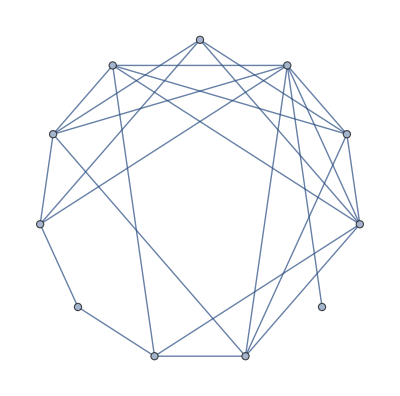
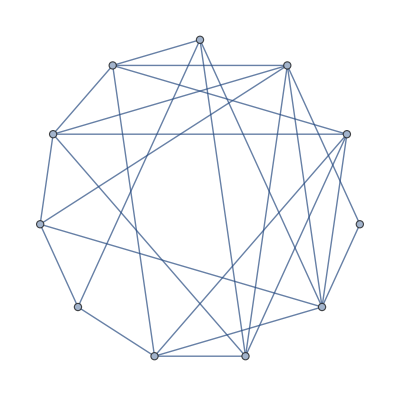
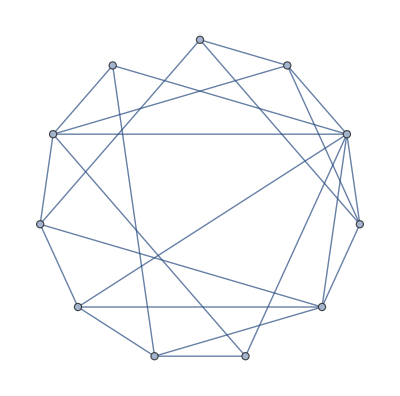
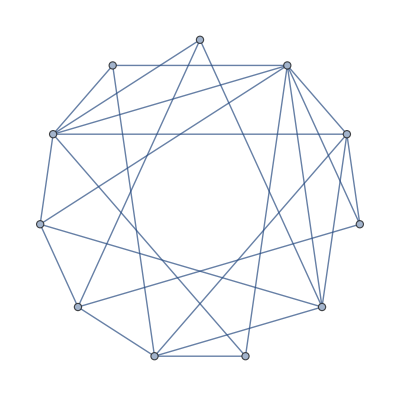
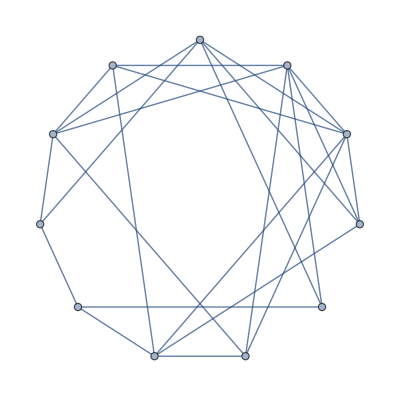
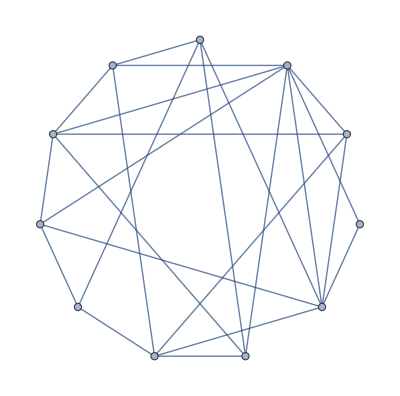
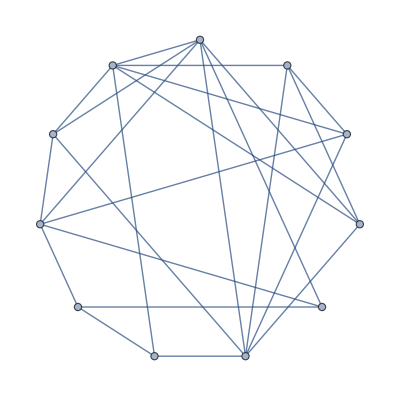
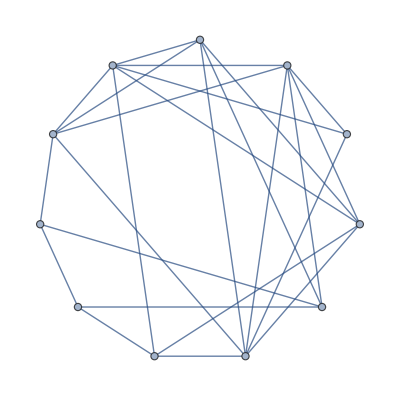
{{{78,-Graphics-},1},{{92,-Graphics-},1},{{94,-Graphics-},1},{{98,-Graphics-},1},{{110,-Graphics-},1},{{116,-Graphics-},1},{{119,-Graphics-},1},{{120,-Graphics-},2},{{138,-Graphics-},1},{{142,-Graphics-},1},{{149,-Graphics-},1},{{156,-Graphics-},1},{{162,-Graphics-},2},{{179,-Graphics-},1},{{185,-Graphics-},1},{{187,-Graphics-},1},{{188,-Graphics-},1},{{194,-Graphics-},1},{{195,-Graphics-},2},{{198,-Graphics-},1},{{208,-Graphics-},1},{{209,-Graphics-},1},{{210,-Graphics-},3},{{213,-Graphics-},1},{{221,-Graphics-},1},{{232,-Graphics-},1},{{234,-Graphics-},1},{{260,-Graphics-},1},{{264,-Graphics-},1},{{270,-Graphics-},1},{{273,-Graphics-},1},{{276,-Graphics-},1},{{278,-Graphics-},1},{{280,-Graphics-},1},{{282,-Graphics-},1},{{288,-Graphics-},1},{{290,-Graphics-},2},{{300,-Graphics-},2},{{301,-Graphics-},1},{{303,-Graphics-},1},{{304,-Graphics-},1},{{308,-Graphics-},1},{{310,-Graphics-},1},{{312,-Graphics-},1},{{317,-Graphics-},1},{{318,-Graphics-},1},{{328,-Graphics-},1},{{330,-Graphics-},1},{{336,-Graphics-},1},{{347,-Graphics-},1},{{354,-Graphics-},1},{{360,-Graphics-},3},{{367,-Graphics-},1},{{368,-Graphics-},1},{{378,-Graphics-},1},{{380,-Graphics-},1},{{387,-Graphics-},1},{{391,-Graphics-},2},{{394,-Graphics-},1},{{395,-Graphics-},1},{{402,-Graphics-},1},{{405,-Graphics-},1},{{406,-Graphics-},1},{{414,-Graphics-},1},{{420,-Graphics-},1},{{424,-Graphics-},2},{{425,-Graphics-},1},{{432,-Graphics-},1},{{433,-Graphics-},1},{{436,-Graphics-},1},{{443,-Graphics-},1},{{446,-Graphics-},1},{{450,-Graphics-},1},{{459,-Graphics-},1},{{465,-Graphics-},2},{{468,-Graphics-},1},{{474,-Graphics-},1},{{478,-Graphics-},1},{{480,-Graphics-},2},{{484,-Graphics-},1},{{495,-Graphics-},1},{{498,-Graphics-},2},{{499,-Graphics-},1},{{510,-Graphics-},1},{{518,-Graphics-},1},{{522,-Graphics-},1},{{528,-Graphics-},1},{{540,-Graphics-},1},{{542,-Graphics-},1},{{544,-Graphics-},1},{{552,-Graphics-},1},{{553,-Graphics-},1},{{555,-Graphics-},2},{{560,-Graphics-},2},{{564,-Graphics-},1},{{570,-Graphics-},1},{{581,-Graphics-},1},{{582,-Graphics-},1},{{586,-Graphics-},1},{{598,-Graphics-},1},{{600,-Graphics-},1},{{605,-Graphics-},1},{{606,-Graphics-},1},{{608,-Graphics-},1},{{610,-Graphics-},1},{{614,-Graphics-},1},{{624,-Graphics-},1},{{628,-Graphics-},1},{{632,-Graphics-},1},{{638,-Graphics-},1},{{646,-Graphics-},1},{{656,-Graphics-},1},{{664,-Graphics-},1},{{668,-Graphics-},1},{{672,-Graphics-},1},{{674,-Graphics-},1},{{687,-Graphics-},1},{{692,-Graphics-},1},{{714,-Graphics-},2},{{726,-Graphics-},1},{{733,-Graphics-},1},{{736,-Graphics-},1},{{750,-Graphics-},1},{{762,-Graphics-},1},{{769,-Graphics-},1},{{777,-Graphics-},1},{{780,-Graphics-},1},{{786,-Graphics-},3},{{798,-Graphics-},1},{{800,-Graphics-},1},{{806,-Graphics-},1},{{812,-Graphics-},1},{{813,-Graphics-},1},{{816,-Graphics-},1},{{837,-Graphics-},1},{{840,-Graphics-},1},{{852,-Graphics-},2},{{866,-Graphics-},1},{{867,-Graphics-},1},{{880,-Graphics-},1},{{885,-Graphics-},1},{{888,-Graphics-},1},{{896,-Graphics-},1},{{918,-Graphics-},1},{{948,-Graphics-},1},{{952,-Graphics-},1},{{955,-Graphics-},1},{{984,-Graphics-},1},{{1001,-Graphics-},1},{{1020,-Graphics-},1},{{1040,-Graphics-},1},{{1087,-Graphics-},1},{{1102,-Graphics-},1},{{1128,-Graphics-},1},{{1323,-Graphics-},1},{{1332,-Graphics-},1},{{1350,-Graphics-},1},{{1357,-Graphics-},1},{{1360,-Graphics-},1},{{1443,-Graphics-},1},{{1466,-Graphics-},1},{{1620,-Graphics-},1},{{1680,-Graphics-},1},{{1743,-Graphics-},1},{{1752,-Graphics-},1},{{1764,-Graphics-},2},{{1809,-Graphics-},1},{{1812,-Graphics-},1},{{1869,-Graphics-},1},{{1890,-Graphics-},1},{{1932,-Graphics-},1},{{2079,-Graphics-},1},{{2484,-Graphics-},1},{{2502,-Graphics-},1},{{2745,-Graphics-},1},{{2835,-Graphics-},1},{{3456,-Graphics-},1},{{3465,-Graphics-},1},{{4536,-Graphics-},1}}

```mathematica
Monitor[Tally[Flatten[With[
{max=11},
With[{edges1=Table[SetsToEdges[MergeSets[{{1,3},{2},{4},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges2=Table[SetsToEdges[MergeSets[{{1,4},{2},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges3=Table[SetsToEdges[MergeSets[{{1},{2,4},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges4=Table[SetsToEdges[MergeSets[{{1},{2,5},{3},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges5=Table[SetsToEdges[MergeSets[{{1},{2},{3,5},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}]
},
Table[
With[{g=EdgeDelete[CompleteGraph[max],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]},
{ChromaticPolynomial[g,4]/24,g}]
,{e1,RandomSample[edges1,5]}
,{e2,RandomSample[edges2,5]}
,{e3,RandomSample[edges3,2]}
,{e4,RandomSample[edges4,2]}
,{e5,RandomSample[edges5,2]}
]
]
],4],#1[[1]]==#2[[1]]&]//Sort,{e1,e2,e3,e4,e5}
]
```

```mathematica
Flatten[With[
{max=11},
With[{edges1=Table[SetsToEdges[MergeSets[{{1,3},{2},{4},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges2=Table[SetsToEdges[MergeSets[{{1,4},{2},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges3=Table[SetsToEdges[MergeSets[{{1},{2,4},{3},{5}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges4=Table[SetsToEdges[MergeSets[{{1},{2,5},{3},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}],
edges5=Table[SetsToEdges[MergeSets[{{1},{2},{3,5},{4}},sets+5]],{sets,KSetPartitions[Range[max-5],4]}]
},
Table[
With[{g=EdgeDelete[CompleteGraph[max],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]},
{ChromaticPolynomial[g,4]/24,g}]
,{e1,RandomSample[edges1,2]}
,{e2,RandomSample[edges2,2]}
,{e3,RandomSample[edges3,2]}
,{e4,RandomSample[edges4,2]}
,{e5,RandomSample[edges5,2]}
]
]
],4]
```

{{828,-Graphics-},{687,-Graphics-},{510,-Graphics-},{452,-Graphics-},{364,-Graphics-},{757,-Graphics-},{906,-Graphics-},{884,-Graphics-},{210,-Graphics-},{496,-Graphics-},{252,-Graphics-},{536,-Graphics-},{540,-Graphics-},{124,-Graphics-},{672,-Graphics-},{422,-Graphics-},{2196,-Graphics-},{864,-Graphics-},{1392,-Graphics-},{1305,-Graphics-},{678,-Graphics-},{1560,-Graphics-},{1623,-Graphics-},{1623,-Graphics-},{675,-Graphics-},{308,-Graphics-},{498,-Graphics-},{747,-Graphics-},{307,-Graphics-},{461,-Graphics-},{1248,-Graphics-},{968,-Graphics-}}